## NaCs 1Σ Hamiltonian, only N and m_N terms

## Setup

### Helper functions

```mathematica
kp[a_,b_]:=KroneckerProduct[a,b](*shorthand Kronecker product*)
conj=Complex[a_,b_]->Complex[a,-b];(*shorthand complex conjugate*)
```

### Constants and units

#### Definition

Specifying all constants. The tunable parameters are in the ‘experiment’ association.

```mathematica
units=Association[cm->Quantity[1,"Centimeters"],um->Quantity[1,"Micrometers"],nm->Quantity[1,"Nanometers"],Hz->Quantity[1,"Hertz"],kHz->Quantity[1,"Kilohertz"],MHz->Quantity[1,"Megahertz"],GHz->Quantity[1,"Gigahertz"],THz->Quantity[1,"Terahertz"],icm->Quantity[1,("Centimeters")^-1],Debye->Quantity[1,"Debyes"],Gauss->Quantity[1,"Gauss"],mV->Quantity[1,"Millivolts"],V->Quantity[1,"Volts"]];
fundamental=Association[ϵ0->Quantity["Permittivity of free space"],ℏ->Quantity["ReducedPlanckConstant"],h->Quantity["PlanckConstant"],μB->Quantity["BohrMagneton"],μN->Quantity["NuclearMagneton"],a0->Quantity[1,"BohrRadius"]];
polarizability=Association[αpar->1872.12,αperp->467.038,Δ->αpar-αperp,α0->(αpar+2αperp)/3]/.units/.fundamental;
nacs=Association[I1->3/2,I2->7/2,Bv->h 1.7396 GHz,eQq1->-h 97 kHz,eQq2->h 150 kHz,c1->h 14.2 Hz,c2->h 854.5 Hz,c3->h 105.6 Hz,c4->h 3941.8 Hz,gr->0,g1->1.478,g2->0.738,σ1->0.0006392,σ2->0.0062787,d0->4.6 Debye]/.units/.fundamental;
krb=Association[Bv->h 1.11395 GHz,eQq1->h 450 kHz,eQq2->-h 1.41 MHz,c1->-h 24.1 Hz,c2->h 420.1 Hz,c3->h 0 Hz,c4->-h 2030.4 Hz,gr->0,g1->-0.324,g2->1.834,σ1->1321 10^-6,σ2->3469 10^-6,d0->1 Debye]/.units/.fundamental;
experiment=Association[r->2.6 um,θh->(π-ArcCos[1/√3])/2,θq->π/2-ArcCos[1/√3],U->h 10 MHz,B0->860 Gauss,E0->10^-8 mV/cm,θB->0,ϕB->0,θE->0,ϕE->0]/.units/.fundamental;
```

#### Default values

Defining which constants are used in the code below.

```mathematica
molecule=nacs;
constants=Association[{units,fundamental,polarizability,molecule,experiment}];
```

### Hilbert space

Defines the single particle Hilbert spaces. For each state in the Hilbert space, there is an associated label with its quantum numbers.

#### Single particle

```mathematica
nM=2; (*maximum rotational angular momentum N*)
nℋ1=Sum[2N+1,{N,0,nM}]; (*number of states in the Hilbert space*)
ℋ1=IdentityMatrix[nℋ1];(*Single particle Hilbert space.*)
sℋ1=Partition[ℋ1,{nℋ1,1}][[1]];(*States in the single particle Hilbert space. These are column vectors with a single 1.*)
lℋ1=Flatten[Table[{n,m},{n,0,nM},{m,-n,n}],1];(*List of state labels. These are strings of|N,m⟩ for all possible values of N and m*)
yℋ1=Flatten[Table[SphericalHarmonicY[n,m,θ,ϕ],{n,0,nM},{m,-n,n}],1];(*List of spherical harmonics Subscript[Y, n,m] for all possible values of N and m*)
s2lℋ1=AssociationThread[sℋ1->lℋ1] (*Association between states and labels*);
l2sℋ1=AssociationThread[lℋ1->sℋ1]; 
l2yℋ1=AssociationThread[lℋ1->yℋ1]; 
y2lℋ1=AssociationThread[yℋ1->lℋ1];
```

### Polarization

#### Jones matrices

Defines the tweezer polarization seen by the molecule, and calculates the angle between the quantization axis and the array.

```mathematica
{θ,ϕ,θd}=.;
qwp[θ_]=Exp[-(ⅈ π)/4]({{Cos[θ]^2+ⅈ Sin[θ]^2, (1-ⅈ) Sin[θ]Cos[θ]}, {(1-ⅈ) Sin[θ]Cos[θ], Sin[θ]^2+ⅈ Cos[θ]^2}});(*quarter waveplate Jones matrix*)
hwp[θ_]=Exp[-(ⅈ π)/2]({{Cos[θ]^2-Sin[θ]^2, 2Cos[θ]Sin[θ]}, {2Cos[θ]Sin[θ], Sin[θ]^2-Cos[θ]^2}});(*half waveplate Jones matrix*)
lpr[η_,θ_]=Exp[-(ⅈ η)/2]({{Cos[θ]^2+Exp[ⅈ η] Sin[θ]^2, (1-Exp[ⅈ η])Cos[θ]Sin[θ]}, {(1-Exp[ⅈ η])Cos[θ]Sin[θ], Sin[θ]^2+Exp[ⅈ η] Cos[θ]^2}});(*linear phase retarder Jones matrix*)

jH=({{1}, {0}});jV=({{0}, {1}});jL=1/(√2)({{1}, {ⅈ}});jR=1/(√2)({{1}, {-ⅈ}});(*Jones vectors for horizontal, vertical, LCP, and RCP light*)
jF[θh_,θq_]=FullSimplify[Flatten[hwp[θh].qwp[θq].jH],Assumptions->{0<=θh<2π,0<=θq<2π}];(*Jones vector seen by molecules*)

pEllipse[θh_,θq_]=FullSimplify[ComplexExpand[Re[jF[θh,θq]Exp[-ⅈ t]]],Assumptions->{t>0,0<=θh<2π,0<=θq<2π}];(*Visualization of the polarization ellipse*)
θd[θh_,θq_]:=ArcCos[Sin[2θh-θq]](*Angle between minor axis and array*)
```

#### Polarizability

```mathematica
{ϵ,n1,m1,n2,m2}=.;
αxyz=({{αperp, 0, 0}, {0, αperp, 0}, {0, 0, αpar}});(*Polarizability tensor in the molecular frame. It is diagonal for a linear molecule*)
Rx=RotationMatrix[-θ,{1,0,0}];(*testing putting a minus sign in the rotation matrices to match Zare, application 8 of chapter 3*)
Ry=RotationMatrix[-θ,{0,1,0}];
Rz=RotationMatrix[-ϕ,{0,0,1}];
ϵ[θh_,θq_]={Append[jF[θh,θq],0]}ᵀ;(*Jones vector seen by the molecule, expressed in 3D coordinates*)
αXYZ=Rzᵀ.Ryᵀ.αxyz.Ry.Rz;
```

```mathematica
meα[{Nb_,mb_},{Nk_,mk_}]:=Integrate[SphericalHarmonicY[Nb,mb,θ,ϕ]*SphericalHarmonicY[Nk,mk,θ,ϕ]αXYZ Sin[θ],{θ,0,π},{ϕ,0,2π}];
```

```mathematica
srAC[{n1_,m1_},{n2_,m2_}]:=(n1==n2)∧(m1==m2∨Abs[m1-m2]==2)
```

```mathematica
$Assumptions=αpar ∈ Reals && αperp ∈ Reals;
```

```mathematica
β[θ_,ϕ_]=-U/α0((ϵ[θh,θq]ᵀ/.Complex[a_,b_]->Complex[a,-b]).αXYZ.ϵ[θh,θq]-(αpar+2αperp)/3//FullSimplify)[[1,1]]/.(αpar-αperp)->Δ;(*Differential light shift relative to N=0. The rotation matrices express the polarizability tensor in the lab frame.*)
```

### Hamiltonians

```mathematica
Hacℋ1=SparseArray[ParallelTable[If[srAC[lℋ1[[i]],lℋ1[[j]]],Integrate[(yℋ1[[i]]/.conj)yℋ1[[j]]β[θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π},Assumptions->{θh>0,θq>0,Δ>0}],0],{i,1,nℋ1},{j,1,nℋ1}]];
```

### Eigenvalues

```mathematica
nRanges=Table[Flatten[Select[lℋ1,#[[1]]==n&]/.PositionIndex[lℋ1]],{n,0,nM}];
```

```mathematica
HacNs=Table[FullSimplify[α0/(U Δ)Normal[Hacℋ1[[nRanges[[n+1]],nRanges[[n+1]]]]]],{n,0,nM}];
```

```mathematica
eigs[n_]:=Module[{evals,evecs},{evals,evecs}=Eigensystem[HacNs[[1+n]]];
evals=FullSimplify[PowerExpand[FullSimplify[evals,Assumptions->{0<=θh<2π,0<=θq<2π}]],Assumptions->{0<=θh<2π,0<=θq<2π}];
evecs=FullSimplify[evecs,Assumptions->{0<=θh<2π,0<=θq<2π}];
{evals,evecs}
]
```

```mathematica
eigsN=ParallelTable[eigs[n],{n,0,nM}];
```

```mathematica
Chop[N[Table[FullSimplify[eigsN[[n+1,1]]/.{θq->experiment[θq],θh->experiment[θh]}],{n,0,nM}]]]
```

{{0},{0.133333,0,-0.133333},{-0.0952381,0,0.0952381,-0.109971,0.109971}}

```mathematica
magicStates=Table[With[{vals=eigsN[[n+1,1]],vecs=eigsN[[n+1,2]]},vecs[[Position[FullSimplify[vals/.{θq->π/2-experiment[θq],θh->0}],0][[1,1]]]]],{n,0,nM}];
magicStates=Table[Flatten[ReplacePart[ReplacePart[nRanges,{i_,j_}->0],(n+1)->magicStates[[n+1]]]],{n,0,nM}]
```

{{1,0,0,0,0,0,0,0,0},{0,-ⅇ^(4 ⅈ θh-2 ⅈ θq),0,1,0,0,0,0,0},{0,0,0,0,0,ⅇ^(4 ⅈ θh-2 ⅈ θq),0,1,0}}

```mathematica
ParallelEvaluate[Off[ClebschGordan::tri]];
ParallelEvaluate[Off[ClebschGordan::phy]];
Off[ClebschGordan::tri];
Off[ClebschGordan::phy];
meE[{Nb_,Mb_},{Nk_,Mk_},q_:0]:=(-1)^Mb √((2Nk+1)(2Nb+1))ThreeJSymbol[{Nb,-Mb},{1,q},{Nk,Mk}]ThreeJSymbol[{Nb,0},{1,0},{Nk,0}];
He1=.;He1[q_]:=ParallelTable[With[{to=lℋ1[[i]],from=lℋ1[[j]]},If[Abs[to[[2]]-from[[2]]]<=1&&Abs[to[[1]]-from[[1]]]==1,meE[to,from,q],0]],{i,1,nℋ1},{j,1,nℋ1}];
He1s=Table[He1[q],{q,-1,1}];
```

```mathematica
magicCouplings=Table[(magicStates[[n+2]]/.conj).He1[q].magicStates[[n+1]],{n,0,nM-1},{q,-1,1}];
```

```mathematica
TableForm[FullSimplify[magicCouplings],TableHeadings->{{"N: 0→1","N: 1→2","N: 2→3","N: 3→4"},{"q=-1","q=0","q=1"}}]
```

| q=-1 | q=0 | q=1
N: 0→1 | -ⅇ^(-4 ⅈ θh+2 ⅈ θq)/(√3) | 0 | 1/(√3)
N: 1→2 | 0 | 0 | 0

```mathematica
evecs=Table[Flatten[ReplacePart[ReplacePart[nRanges,{i_,j_}->0],(n+1)->eigsN[[n+1,2,m]]]],{n,0,nM},{m,1,2 n+1}];
```

```mathematica
c21=With[{nu=2,nl=1},Table[(evecs[[nu+1,mu]]/.conj).He1[q].evecs[[nl+1,ml]],{ml,2 nl +1},{mu,2 nu+1},{q,-1,1}]];
```

```mathematica
c21[[3]]
```

{{√(2/5) ⅇ^(-4 ⅈ θh+2 ⅈ θq),0,√(2/5)},{0,2/(√5),0},{0,0,0},{-√(2/5) ⅇ^(-4 ⅈ θh+2 ⅈ θq)+(√(2/5) ⅇ^(-4 ⅈ θh+2 ⅈ θq) (2 ⅇ^(-2 ⅈ θq)-√((3+ⅇ^(-4 ⅈ θq)) (1+3 ⅇ^(-4 ⅈ θq)))))/(3 (1+ⅇ^(-4 ⅈ θq))),0,√(2/5)-(√(2/5) (2 ⅇ^(-2 ⅈ θq)-√((3+ⅇ^(-4 ⅈ θq)) (1+3 ⅇ^(-4 ⅈ θq)))))/(3 (1+ⅇ^(-4 ⅈ θq)))},{-√(2/5) ⅇ^(-4 ⅈ θh+2 ⅈ θq)+(√(2/5) ⅇ^(-4 ⅈ θh+2 ⅈ θq) (2 ⅇ^(-2 ⅈ θq)+√((3+ⅇ^(-4 ⅈ θq)) (1+3 ⅇ^(-4 ⅈ θq)))))/(3 (1+ⅇ^(-4 ⅈ θq))),0,√(2/5)-(√(2/5) (2 ⅇ^(-2 ⅈ θq)+√((3+ⅇ^(-4 ⅈ θq)) (1+3 ⅇ^(-4 ⅈ θq)))))/(3 (1+ⅇ^(-4 ⅈ θq)))}}

```mathematica
c10[[1]]
```

{{0,1/(√3),0},{ⅇ^(-4 ⅈ θh+2 ⅈ θq)/(√3),0,1/(√3)},{-ⅇ^(-4 ⅈ θh+2 ⅈ θq)/(√3),0,1/(√3)}}

```mathematica
eigsN[[2,2,2]]
```

{ⅇ^(4 ⅈ θh-2 ⅈ θq),0,1}

# STOP

```mathematica
SphericalPlot3D[Abs[yℋ1.magicStates[[3]]/.{θh->experiment[θh],θq->experiment[θq]}]^2,{θ,0,π},{ϕ,0,2π},AxesLabel->{"x","y","z"},PlotRange->All]
```

-Graphics3D-

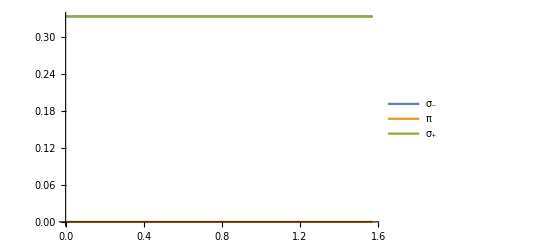

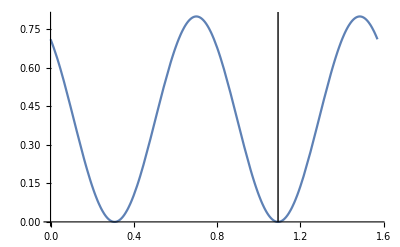

```mathematica
Plot[Evaluate@(Abs[magicCouplings[[1,#]]]^2&/@{1,2,3}/.{θq->experiment[θq]}),{θh,0,π/2},PlotLegends->{"σ_-","π","σ_+"}]
```

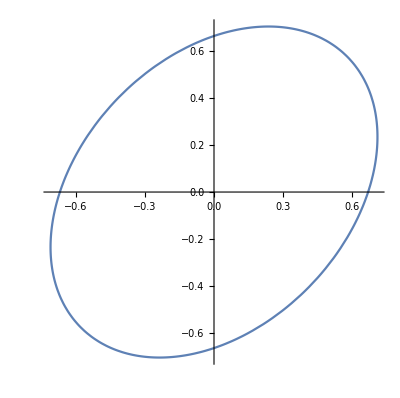

```mathematica
ParametricPlot[pEllipse[0.697,experiment[θq]],{t,0,2π}]
```

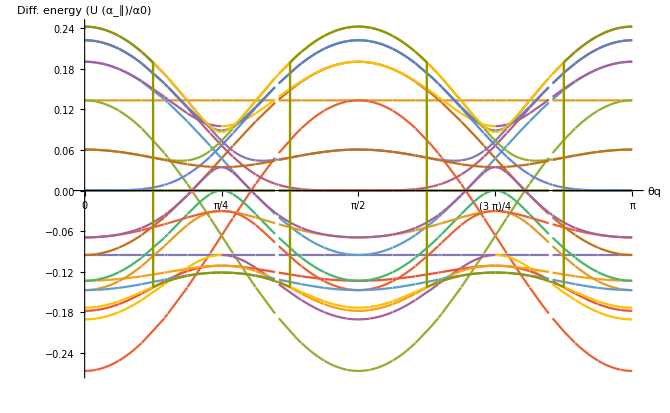

```mathematica
Plot[Evaluate@Table[(eigsN[[n+1,1]]/.{θh->0}),{n,0,nM}],{θq,0,π},AxesLabel->{"θq","Diff. energy (U (α_∥)/α0)"},Ticks->{Range[0,π,π/4],Automatic},ImageSize->Medium,Exclusions->True,Epilog->{PointSize[Large],Pink,Point[{experiment[θq],0}]}]
```

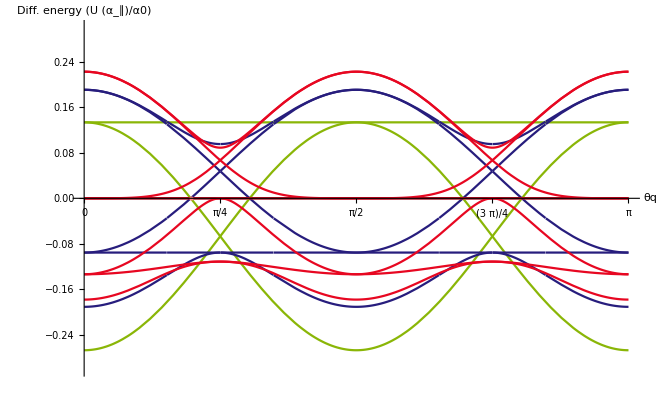

```mathematica
Show[Table[Plot[Evaluate@(eigsN[[n+1,1]]/.{θh->0}),{θq,0,π},AxesLabel->{"θq","Diff. energy (U (α_∥)/α0)"},Ticks->{Range[0,π,π/4],Automatic},PlotStyle->ColorData[3,3n+1],PlotRange->{-0.3,0.3},ImageSize->Medium,Exclusions->True,Epilog->{PointSize[Large],Pink,Point[{experiment[θq],0}]}],{n,0,nM-1}]]
```

```mathematica
Table[{StringForm["n=``",n],ColorData[3,3n+1]},{n,0,nM-1}]
```

{{n=0,RGBColor[0., 0., 0.]},{n=1,RGBColor[0.5411764705882353, 0.7137254901960784, 0.027450980392156862]},{n=2,RGBColor[0.15294117647058825, 0.11372549019607843, 0.49019607843137253]},{n=3,RGBColor[0.9058823529411765, 0.027450980392156862, 0.12941176470588237]}}

```mathematica
ColorData[3]
```

ColorDataFunction[…]

```mathematica
vecsN=Table[Flatten[ReplacePart[ReplacePart[nRanges,{i_,j_}->0],(n+1)->#]]&/@eigsN[[n+1,2]],{n,0,nM}]
lEig=Flatten[Table[{n,FromLetterNumber[m]},{n,0,nM},{m,1,2n+1}],1];
```

{{{1,0,0,0,0,0,0,0,0}},{{0,0,1,0,0,0,0,0,0},{0,ⅇ^(4 ⅈ θh-2 ⅈ θq),0,1,0,0,0,0,0},{0,-ⅇ^(4 ⅈ θh-2 ⅈ θq),0,1,0,0,0,0,0}},{{0,0,0,0,-ⅇ^(8 ⅈ θh-4 ⅈ θq),0,0,0,1},{0,0,0,0,0,-ⅇ^(4 ⅈ θh-2 ⅈ θq),0,1,0},{0,0,0,0,0,ⅇ^(4 ⅈ θh-2 ⅈ θq),0,1,0},{0,0,0,0,ⅇ^(8 ⅈ θh-4 ⅈ θq),0,(√(2/3) ⅇ^(4 ⅈ θh-2 ⅈ θq) (2 ⅇ^(2 ⅈ θq)-√((3+ⅇ^(4 ⅈ θq)) (1+3 ⅇ^(4 ⅈ θq)))))/(1+ⅇ^(4 ⅈ θq)),0,1},{0,0,0,0,ⅇ^(8 ⅈ θh-4 ⅈ θq),0,(√(2/3) ⅇ^(4 ⅈ θh-2 ⅈ θq) (2 ⅇ^(2 ⅈ θq)+√((3+ⅇ^(4 ⅈ θq)) (1+3 ⅇ^(4 ⅈ θq)))))/(1+ⅇ^(4 ⅈ θq)),0,1}}}

```mathematica
l2vec=AssociationThread[lEig->Flatten[vecsN,1]];
```

```mathematica
He1
```

```mathematica
stateCoupling[{n_,l_}]:=Table[({l2vec[{n+1,FromLetterNumber[lett]}]}.He1s[[2+q]].{l2vec[{n,l}]}ᵀ)[[1,1]],{lett,1,2*(n+1)+1},{q,-1,1}]
```

```mathematica
Normalize/@N[FullSimplify[stateCoupling[{3,"d"}]/.{θh->experiment[θh],θq->experiment[θq]}]]
```

$Aborted

```mathematica
nM
```

4

```mathematica
l2vec[{1,"b"}]
```

{0,ⅇ^(-4 ⅈ θh+2 ⅈ θq),0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
l2vec
```

<|{0,a}→{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,a}→{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,b}→{0,ⅇ^(-4 ⅈ θh+2 ⅈ θq),0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,c}→{0,-ⅇ^(-4 ⅈ θh+2 ⅈ θq),0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{2,a}→{0,0,0,0,-ⅇ^(-8 ⅈ θh+4 ⅈ θq),0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{2,b}→{0,0,0,0,0,-ⅇ^(-4 ⅈ θh+2 ⅈ θq),0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{2,c}→{0,0,0,0,0,ⅇ^(-4 ⅈ θh+2 ⅈ θq),0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{2,d}→{0,0,0,0,ⅇ^(-8 ⅈ θh+4 ⅈ θq),0,-(ⅇ^(-4 ⅈ θh) (-2 ⅇ^(2 ⅈ θq)+√(3+10 ⅇ^(4 ⅈ θq)+3 ⅇ^(8 ⅈ θq))) Sec[2 θq])/(√6),0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{2,e}→{0,0,0,0,ⅇ^(-8 ⅈ θh+4 ⅈ θq),0,(ⅇ^(-4 ⅈ θh) (2 ⅇ^(2 ⅈ θq)+√(3+10 ⅇ^(4 ⅈ θq)+3 ⅇ^(8 ⅈ θq))) Sec[2 θq])/(√6),0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{3,a}→{0,0,0,0,0,0,0,0,0,0,-ⅇ^(-8 ⅈ θh+4 ⅈ θq),0,0,0,1,0,0,0,0,0,0,0,0,0,0},{3,b}→{0,0,0,0,0,0,0,0,0,-ⅇ^(-12 ⅈ θh+6 ⅈ θq),0,(ⅇ^(-2 ⅈ (8 θh+θq)) (2 ⅇ^(8 ⅈ (θh+θq)) (-4+3 Cos[2 θq])+4 √(ⅇ^(16 ⅈ (θh+θq)) (7-6 Cos[2 θq]+3 Cos[4 θq]))))/(√15 (1+ⅇ^(4 ⅈ θq))),0,(ⅇ^(-4 ⅈ (3 θh+θq)) (-2 ⅇ^(8 ⅈ (θh+θq)) (-4+3 Cos[2 θq])-4 √(ⅇ^(16 ⅈ (θh+θq)) (7-6 Cos[2 θq]+3 Cos[4 θq]))))/(√15 (1+ⅇ^(4 ⅈ θq))),0,1,0,0,0,0,0,0,0,0,0},{3,c}→{0,0,0,0,0,0,0,0,0,-ⅇ^(-12 ⅈ θh+6 ⅈ θq),0,(ⅇ^(-2 ⅈ (8 θh+θq)) (2 ⅇ^(8 ⅈ (θh+θq)) (-4+3 Cos[2 θq])-4 √(ⅇ^(16 ⅈ (θh+θq)) (7-6 Cos[2 θq]+3 Cos[4 θq]))))/(√15 (1+ⅇ^(4 ⅈ θq))),0,(ⅇ^(-4 ⅈ (3 θh+θq)) (-2 ⅇ^(8 ⅈ (θh+θq)) (-4+3 Cos[2 θq])+4 √(ⅇ^(16 ⅈ (θh+θq)) (7-6 Cos[2 θq]+3 Cos[4 θq]))))/(√15 (1+ⅇ^(4 ⅈ θq))),0,1,0,0,0,0,0,0,0,0,0},{3,d}→{0,0,0,0,0,0,0,0,0,ⅇ^(-12 ⅈ θh+6 ⅈ θq),0,(ⅇ^(-2 ⅈ (8 θh+θq)) (2 ⅇ^(8 ⅈ (θh+θq)) (4+3 Cos[2 θq])-4 √(ⅇ^(16 ⅈ (θh+θq)) (7+6 Cos[2 θq]+3 Cos[4 θq]))))/(√15 (1+ⅇ^(4 ⅈ θq))),0,(ⅇ^(-4 ⅈ (3 θh+θq)) (2 ⅇ^(8 ⅈ (θh+θq)) (4+3 Cos[2 θq])-4 √(ⅇ^(16 ⅈ (θh+θq)) (7+6 Cos[2 θq]+3 Cos[4 θq]))))/(√15 (1+ⅇ^(4 ⅈ θq))),0,1,0,0,0,0,0,0,0,0,0},{3,e}→{0,0,0,0,0,0,0,0,0,ⅇ^(-12 ⅈ θh+6 ⅈ θq),0,(ⅇ^(-2 ⅈ (8 θh+θq)) (2 ⅇ^(8 ⅈ (θh+θq)) (4+3 Cos[2 θq])+4 √(ⅇ^(16 ⅈ (θh+θq)) (7+6 Cos[2 θq]+3 Cos[4 θq]))))/(√15 (1+ⅇ^(4 ⅈ θq))),0,(ⅇ^(-4 ⅈ (3 θh+θq)) (2 ⅇ^(8 ⅈ (θh+θq)) (4+3 Cos[2 θq])+4 √(ⅇ^(16 ⅈ (θh+θq)) (7+6 Cos[2 θq]+3 Cos[4 θq]))))/(√15 (1+ⅇ^(4 ⅈ θq))),0,1,0,0,0,0,0,0,0,0,0},{3,f}→{0,0,0,0,0,0,0,0,0,0,ⅇ^(-8 ⅈ θh+4 ⅈ θq),0,-(2 ⅇ^(-4 ⅈ (3 θh+θq)) (-√2 ⅇ^(8 ⅈ (θh+θq))+√(ⅇ^(16 ⅈ (θh+θq)) (17+15 Cos[4 θq]))))/(√15 (1+ⅇ^(4 ⅈ θq))),0,1,0,0,0,0,0,0,0,0,0,0},{3,g}→{0,0,0,0,0,0,0,0,0,0,ⅇ^(-8 ⅈ θh+4 ⅈ θq),0,(2 ⅇ^(-4 ⅈ (3 θh+θq)) (√2 ⅇ^(8 ⅈ (θh+θq))+√(ⅇ^(16 ⅈ (θh+θq)) (17+15 Cos[4 θq]))))/(√15 (1+ⅇ^(4 ⅈ θq))),0,1,0,0,0,0,0,0,0,0,0,0},{4,a}→{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅇ^(-12 ⅈ θh+6 ⅈ θq),0,(ⅇ^(-16 ⅈ θh) (ⅇ^(4 ⅈ (2 θh+θq)) (5-4 Sec[2 θq])+2 √(ⅇ^(8 ⅈ (2 θh+θq)) (15-10 Cos[2 θq]+11 Cos[4 θq])) Sec[2 θq]))/(3 √7),0,(ⅇ^(-2 ⅈ (6 θh+θq)) (-2 √(ⅇ^(8 ⅈ (2 θh+θq)) (15-10 Cos[2 θq]+11 Cos[4 θq])) Sec[2 θq]+ⅇ^(4 ⅈ (2 θh+θq)) (-5+4 Sec[2 θq])))/(3 √7),0,1,0},{4,b}→{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅇ^(-12 ⅈ θh+6 ⅈ θq),0,(ⅇ^(-16 ⅈ θh) (ⅇ^(4 ⅈ (2 θh+θq)) (5-4 Sec[2 θq])-2 √(ⅇ^(8 ⅈ (2 θh+θq)) (15-10 Cos[2 θq]+11 Cos[4 θq])) Sec[2 θq]))/(3 √7),0,(ⅇ^(-2 ⅈ (6 θh+θq)) (2 √(ⅇ^(8 ⅈ (2 θh+θq)) (15-10 Cos[2 θq]+11 Cos[4 θq])) Sec[2 θq]+ⅇ^(4 ⅈ (2 θh+θq)) (-5+4 Sec[2 θq])))/(3 √7),0,1,0},{4,c}→{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅇ^(-12 ⅈ θh+6 ⅈ θq),0,(ⅇ^(-16 ⅈ θh) (-2 √(ⅇ^(8 ⅈ (2 θh+θq)) (15+10 Cos[2 θq]+11 Cos[4 θq])) Sec[2 θq]+ⅇ^(4 ⅈ (2 θh+θq)) (5+4 Sec[2 θq])))/(3 √7),0,(ⅇ^(-2 ⅈ (6 θh+θq)) (-2 √(ⅇ^(8 ⅈ (2 θh+θq)) (15+10 Cos[2 θq]+11 Cos[4 θq])) Sec[2 θq]+ⅇ^(4 ⅈ (2 θh+θq)) (5+4 Sec[2 θq])))/(3 √7),0,1,0},{4,d}→{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅇ^(-12 ⅈ θh+6 ⅈ θq),0,(ⅇ^(-16 ⅈ θh) (2 √(ⅇ^(8 ⅈ (2 θh+θq)) (15+10 Cos[2 θq]+11 Cos[4 θq])) Sec[2 θq]+ⅇ^(4 ⅈ (2 θh+θq)) (5+4 Sec[2 θq])))/(3 √7),0,(ⅇ^(-2 ⅈ (6 θh+θq)) (2 √(ⅇ^(8 ⅈ (2 θh+θq)) (15+10 Cos[2 θq]+11 Cos[4 θq])) Sec[2 θq]+ⅇ^(4 ⅈ (2 θh+θq)) (5+4 Sec[2 θq])))/(3 √7),0,1,0},{4,e}→{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅇ^(-16 ⅈ θh+8 ⅈ θq),0,-(ⅇ^(-20 ⅈ θh+2 ⅈ θq) (6 ⅇ^(4 ⅈ (2 θh+θq))+√2 √(ⅇ^(8 ⅈ (2 θh+θq)) (25+7 Cos[4 θq]))) Sec[2 θq])/(2 √7),0,0,0,(ⅇ^(-12 ⅈ θh) (6 ⅇ^(4 ⅈ (2 θh+θq))+√2 √(ⅇ^(8 ⅈ (2 θh+θq)) (25+7 Cos[4 θq]))))/(√7 (1+ⅇ^(4 ⅈ θq))),0,1},{4,f}→{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅇ^(-16 ⅈ θh+8 ⅈ θq),0,(ⅇ^(-20 ⅈ θh+2 ⅈ θq) (-6 ⅇ^(4 ⅈ (2 θh+θq))+√2 √(ⅇ^(8 ⅈ (2 θh+θq)) (25+7 Cos[4 θq]))) Sec[2 θq])/(2 √7),0,0,0,(ⅇ^(-12 ⅈ θh) (6 ⅇ^(4 ⅈ (2 θh+θq))-√2 √(ⅇ^(8 ⅈ (2 θh+θq)) (25+7 Cos[4 θq]))))/(√7 (1+ⅇ^(4 ⅈ θq))),0,1},{4,g}→{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅇ^(-16 ⅈ θh+8 ⅈ θq),0,(ⅇ^(-4 ⅈ (5 θh-θq)) (56 ⅇ^(4 ⅈ (2 θh+θq))+Root[-80640 ⅇ^(24 ⅈ θh+8 ⅈ θq)-125440 ⅇ^(24 ⅈ θh+12 ⅈ θq)-80640 ⅇ^(24 ⅈ θh+16 ⅈ θq)+(-1872 ⅇ^(16 ⅈ θh+4 ⅈ θq)-6240 ⅇ^(16 ⅈ θh+8 ⅈ θq)-1872 ⅇ^(16 ⅈ θh+12 ⅈ θq)) #1+#1^3&,1]))/(6 √7 (1+ⅇ^(4 ⅈ θq))),0,1/(108 √70 (1+ⅇ^(4 ⅈ θq)))ⅇ^(-2 ⅈ (12 θh+θq)) (-56 ⅇ^(8 ⅈ (2 θh+θq)) (25+9 Cos[4 θq])+40 ⅇ^(4 ⅈ (2 θh+θq)) Root[-80640 ⅇ^(24 ⅈ θh+8 ⅈ θq)-125440 ⅇ^(24 ⅈ θh+12 ⅈ θq)-80640 ⅇ^(24 ⅈ θh+16 ⅈ θq)+(-1872 ⅇ^(16 ⅈ θh+4 ⅈ θq)-6240 ⅇ^(16 ⅈ θh+8 ⅈ θq)-1872 ⅇ^(16 ⅈ θh+12 ⅈ θq)) #1+#1^3&,1]+Root[-80640 ⅇ^(24 ⅈ θh+8 ⅈ θq)-125440 ⅇ^(24 ⅈ θh+12 ⅈ θq)-80640 ⅇ^(24 ⅈ θh+16 ⅈ θq)+(-1872 ⅇ^(16 ⅈ θh+4 ⅈ θq)-6240 ⅇ^(16 ⅈ θh+8 ⅈ θq)-1872 ⅇ^(16 ⅈ θh+12 ⅈ θq)) #1+#1^3&,1]^2) Sec[2 θq],0,(ⅇ^(-12 ⅈ θh) (56 ⅇ^(4 ⅈ (2 θh+θq))+Root[-80640 ⅇ^(24 ⅈ θh+8 ⅈ θq)-125440 ⅇ^(24 ⅈ θh+12 ⅈ θq)-80640 ⅇ^(24 ⅈ θh+16 ⅈ θq)+(-1872 ⅇ^(16 ⅈ θh+4 ⅈ θq)-6240 ⅇ^(16 ⅈ θh+8 ⅈ θq)-1872 ⅇ^(16 ⅈ θh+12 ⅈ θq)) #1+#1^3&,1]))/(6 √7 (1+ⅇ^(4 ⅈ θq))),0,1},{4,h}→{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅇ^(-16 ⅈ θh+8 ⅈ θq),0,(ⅇ^(-4 ⅈ (5 θh-θq)) (56 ⅇ^(4 ⅈ (2 θh+θq))+Root[-80640 ⅇ^(24 ⅈ θh+8 ⅈ θq)-125440 ⅇ^(24 ⅈ θh+12 ⅈ θq)-80640 ⅇ^(24 ⅈ θh+16 ⅈ θq)+(-1872 ⅇ^(16 ⅈ θh+4 ⅈ θq)-6240 ⅇ^(16 ⅈ θh+8 ⅈ θq)-1872 ⅇ^(16 ⅈ θh+12 ⅈ θq)) #1+#1^3&,2]))/(6 √7 (1+ⅇ^(4 ⅈ θq))),0,1/(108 √70 (1+ⅇ^(4 ⅈ θq)))ⅇ^(-2 ⅈ (12 θh+θq)) (-56 ⅇ^(8 ⅈ (2 θh+θq)) (25+9 Cos[4 θq])+40 ⅇ^(4 ⅈ (2 θh+θq)) Root[-80640 ⅇ^(24 ⅈ θh+8 ⅈ θq)-125440 ⅇ^(24 ⅈ θh+12 ⅈ θq)-80640 ⅇ^(24 ⅈ θh+16 ⅈ θq)+(-1872 ⅇ^(16 ⅈ θh+4 ⅈ θq)-6240 ⅇ^(16 ⅈ θh+8 ⅈ θq)-1872 ⅇ^(16 ⅈ θh+12 ⅈ θq)) #1+#1^3&,2]+Root[-80640 ⅇ^(24 ⅈ θh+8 ⅈ θq)-125440 ⅇ^(24 ⅈ θh+12 ⅈ θq)-80640 ⅇ^(24 ⅈ θh+16 ⅈ θq)+(-1872 ⅇ^(16 ⅈ θh+4 ⅈ θq)-6240 ⅇ^(16 ⅈ θh+8 ⅈ θq)-1872 ⅇ^(16 ⅈ θh+12 ⅈ θq)) #1+#1^3&,2]^2) Sec[2 θq],0,(ⅇ^(-12 ⅈ θh) (56 ⅇ^(4 ⅈ (2 θh+θq))+Root[-80640 ⅇ^(24 ⅈ θh+8 ⅈ θq)-125440 ⅇ^(24 ⅈ θh+12 ⅈ θq)-80640 ⅇ^(24 ⅈ θh+16 ⅈ θq)+(-1872 ⅇ^(16 ⅈ θh+4 ⅈ θq)-6240 ⅇ^(16 ⅈ θh+8 ⅈ θq)-1872 ⅇ^(16 ⅈ θh+12 ⅈ θq)) #1+#1^3&,2]))/(6 √7 (1+ⅇ^(4 ⅈ θq))),0,1},{4,i}→{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅇ^(-16 ⅈ θh+8 ⅈ θq),0,(ⅇ^(-4 ⅈ (5 θh-θq)) (56 ⅇ^(4 ⅈ (2 θh+θq))+Root[-80640 ⅇ^(24 ⅈ θh+8 ⅈ θq)-125440 ⅇ^(24 ⅈ θh+12 ⅈ θq)-80640 ⅇ^(24 ⅈ θh+16 ⅈ θq)+(-1872 ⅇ^(16 ⅈ θh+4 ⅈ θq)-6240 ⅇ^(16 ⅈ θh+8 ⅈ θq)-1872 ⅇ^(16 ⅈ θh+12 ⅈ θq)) #1+#1^3&,3]))/(6 √7 (1+ⅇ^(4 ⅈ θq))),0,1/(108 √70 (1+ⅇ^(4 ⅈ θq)))ⅇ^(-2 ⅈ (12 θh+θq)) (-56 ⅇ^(8 ⅈ (2 θh+θq)) (25+9 Cos[4 θq])+40 ⅇ^(4 ⅈ (2 θh+θq)) Root[-80640 ⅇ^(24 ⅈ θh+8 ⅈ θq)-125440 ⅇ^(24 ⅈ θh+12 ⅈ θq)-80640 ⅇ^(24 ⅈ θh+16 ⅈ θq)+(-1872 ⅇ^(16 ⅈ θh+4 ⅈ θq)-6240 ⅇ^(16 ⅈ θh+8 ⅈ θq)-1872 ⅇ^(16 ⅈ θh+12 ⅈ θq)) #1+#1^3&,3]+Root[-80640 ⅇ^(24 ⅈ θh+8 ⅈ θq)-125440 ⅇ^(24 ⅈ θh+12 ⅈ θq)-80640 ⅇ^(24 ⅈ θh+16 ⅈ θq)+(-1872 ⅇ^(16 ⅈ θh+4 ⅈ θq)-6240 ⅇ^(16 ⅈ θh+8 ⅈ θq)-1872 ⅇ^(16 ⅈ θh+12 ⅈ θq)) #1+#1^3&,3]^2) Sec[2 θq],0,(ⅇ^(-12 ⅈ θh) (56 ⅇ^(4 ⅈ (2 θh+θq))+Root[-80640 ⅇ^(24 ⅈ θh+8 ⅈ θq)-125440 ⅇ^(24 ⅈ θh+12 ⅈ θq)-80640 ⅇ^(24 ⅈ θh+16 ⅈ θq)+(-1872 ⅇ^(16 ⅈ θh+4 ⅈ θq)-6240 ⅇ^(16 ⅈ θh+8 ⅈ θq)-1872 ⅇ^(16 ⅈ θh+12 ⅈ θq)) #1+#1^3&,3]))/(6 √7 (1+ⅇ^(4 ⅈ θq))),0,1}|>

```mathematica
FullSimplify[%/.{θq->experiment[θq]}]
```

{{0,0,0},{ⅇ^(-2 ⅈ (2 θh+ArcSec[√3]))/(√5),0,1/(√5)},{-ⅇ^(-2 ⅈ (2 θh+ArcSec[√3]))/(√5),0,1/(√5)},{0,2 √(2/15 (7-4 √3)) ⅇ^(-2 ⅈ (2 θh+ArcSec[√3])),0},{0,-2 √(2/15 (7+4 √3)) ⅇ^(-2 ⅈ (2 θh+ArcSec[√3])),0}}

```mathematica
Table[vecsN[[2,m]].He1[q].vecsN[[1]]ᵀ,{m,1,3},{q,-1,1}]
```

{{{0},{1/(√3)},{0}},{{ⅇ^(-4 ⅈ θh+2 ⅈ θq)/(√3)},{0},{1/(√3)}},{{-ⅇ^(-4 ⅈ θh+2 ⅈ θq)/(√3)},{0},{1/(√3)}}}

```mathematica
lℋ1
```

{{0,0},{1,-1},{1,0},{1,1},{2,-2},{2,-1},{2,0},{2,1},{2,2},{3,-3},{3,-2},{3,-1},{3,0},{3,1},{3,2},{3,3},{4,-4},{4,-3},{4,-2},{4,-1},{4,0},{4,1},{4,2},{4,3},{4,4}}

```mathematica
experiment[θh]//N
```

1.09314

```mathematica
He1[1].{Join[pre,evecs[[-1]],post]}ᵀ
```

{{0},{0},{0},{0},{0},{√(2/7)},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{-1/(√21)},{0},{0},{0},{1/(√3)},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0}}

```mathematica
nRanges[[3+1]]
```

{10,11,12,13,14,15,16}

```mathematica
FullSimplify[evals3/.θq->experiment[θq]]
```

{0,-2/135 (3+2 √6),2/135 (-3+2 √6),-4/(9 √15),4/(9 √15),1/135 (6-4 √6),2/135 (3+2 √6)}

```mathematica
ev=FullSimplify[evecs3[[1]]/.θq->experiment[θq]]
```

{0,-ⅇ^(-4 ⅈ (2 θh+ArcSec[√3])),0,0,0,1,0}

```mathematica
Manipulate[SphericalPlot3D[With[{θh=θh1},Abs[ev.yℋ1[[nRanges[[1+3]]]]]^2],{θ,0,π},{ϕ,0,2π},PlotRange->All],{θh1,0,π}]
```

Part::partw: Part 4 of {{1},{2,3,4},{5,6,7,8,9}} does not exist.

Part::pkspec1: The expression {{1},{2,3,4},{5,6,7,8,9}}⟦4⟧ cannot be used as a part specification.

Part::partw: Part 4 of {{1},{2,3,4},{5,6,7,8,9}} does not exist.

Part::pkspec1: The expression {{1},{2,3,4},{5,6,7,8,9}}⟦4⟧ cannot be used as a part specification.

Part::partw: Part 4 of {{1},{2,3,4},{5,6,7,8,9}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::pkspec1: The expression {{1},{2,3,4},{5,6,7,8,9}}⟦4⟧ cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Part::partd: Part specification nRanges⟦4⟧ is longer than depth of object.

Part::pkspec1: The expression nRanges⟦4⟧ cannot be used as a part specification.

Part::partd: Part specification nRanges⟦4⟧ is longer than depth of object.

Part::pkspec1: The expression nRanges⟦4⟧ cannot be used as a part specification.

Part::partd: Part specification nRanges⟦4⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::pkspec1: The expression nRanges⟦4⟧ cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

```mathematica
FullSimplify[evecs2,Assumptions->{θq∈Reals,θq>0}]
```

{{-ⅇ^(4 ⅈ θq),0,0,0,1},{0,-ⅇ^(2 ⅈ θq),0,1,0},{0,ⅇ^(2 ⅈ θq),0,1,0},{ⅇ^(4 ⅈ θq),0,(ⅇ^(-4 ⅈ θq) (√2 ⅇ^(6 ⅈ θq)-√(ⅇ^(12 ⅈ θq) (5+3 Cos[4 θq]))) Sec[2 θq])/(√3),0,1},{ⅇ^(4 ⅈ θq),0,(ⅇ^(-4 ⅈ θq) (√2 ⅇ^(6 ⅈ θq)+√(ⅇ^(12 ⅈ θq) (5+3 Cos[4 θq]))) Sec[2 θq])/(√3),0,1}}

```mathematica
FullSimplify[((√2 ⅇ^(2 ⅈ θq)+√(ⅇ^(4 ⅈ θq) (5+3 Cos[4 θq]))) Sec[2 θq])/(√3)]
```

```mathematica
FullSimplify[ExpandAll[(((√2 ⅇ^(2 ⅈ θq)+√(ⅇ^(4 ⅈ θq) (5+3 Cos[4 θq]))) Sec[2 θq])/(√3))^2]]
```

1/3 ⅇ^(2 ⅈ θq) (2 √((3+ⅇ^(4 ⅈ θq)) (1+3 ⅇ^(4 ⅈ θq)))+ⅇ^(2 ⅈ θq) (7+3 Cos[4 θq])) Sec[2 θq]^2

```mathematica
evals5
```

{-1/39 ⅇ^(-6 ⅈ θq) √(3 ⅇ^(8 ⅈ θq)+10 ⅇ^(12 ⅈ θq)+3 ⅇ^(16 ⅈ θq)),1/39 ⅇ^(-6 ⅈ θq) √(3 ⅇ^(8 ⅈ θq)+10 ⅇ^(12 ⅈ θq)+3 ⅇ^(16 ⅈ θq)),1/234 ⅇ^(-6 ⅈ θq) Root[-2880 ⅇ^(14 ⅈ θq)-2880 ⅇ^(18 ⅈ θq)-2880 ⅇ^(22 ⅈ θq)+(-528 ⅇ^(8 ⅈ θq)-1200 ⅇ^(12 ⅈ θq)-528 ⅇ^(16 ⅈ θq)) #1-20 ⅇ^(6 ⅈ θq) #1^2+#1^3&,1],1/234 ⅇ^(-6 ⅈ θq) Root[-2880 ⅇ^(14 ⅈ θq)-2880 ⅇ^(18 ⅈ θq)-2880 ⅇ^(22 ⅈ θq)+(-528 ⅇ^(8 ⅈ θq)-1200 ⅇ^(12 ⅈ θq)-528 ⅇ^(16 ⅈ θq)) #1-20 ⅇ^(6 ⅈ θq) #1^2+#1^3&,2],1/234 ⅇ^(-6 ⅈ θq) Root[-2880 ⅇ^(14 ⅈ θq)-2880 ⅇ^(18 ⅈ θq)-2880 ⅇ^(22 ⅈ θq)+(-528 ⅇ^(8 ⅈ θq)-1200 ⅇ^(12 ⅈ θq)-528 ⅇ^(16 ⅈ θq)) #1-20 ⅇ^(6 ⅈ θq) #1^2+#1^3&,3],1/234 ⅇ^(-6 ⅈ θq) Root[675 ⅇ^(12 ⅈ θq)-4230 ⅇ^(14 ⅈ θq)+2925 ⅇ^(16 ⅈ θq)-7380 ⅇ^(18 ⅈ θq)+2925 ⅇ^(20 ⅈ θq)-4230 ⅇ^(22 ⅈ θq)+675 ⅇ^(24 ⅈ θq)+(-213 ⅇ^(8 ⅈ θq)-420 ⅇ^(10 ⅈ θq)-990 ⅇ^(12 ⅈ θq)-420 ⅇ^(14 ⅈ θq)-213 ⅇ^(16 ⅈ θq)) #1+(-15 ⅇ^(4 ⅈ θq)+10 ⅇ^(6 ⅈ θq)-15 ⅇ^(8 ⅈ θq)) #1^2+#1^3&,1],1/234 ⅇ^(-6 ⅈ θq) Root[675 ⅇ^(12 ⅈ θq)-4230 ⅇ^(14 ⅈ θq)+2925 ⅇ^(16 ⅈ θq)-7380 ⅇ^(18 ⅈ θq)+2925 ⅇ^(20 ⅈ θq)-4230 ⅇ^(22 ⅈ θq)+675 ⅇ^(24 ⅈ θq)+(-213 ⅇ^(8 ⅈ θq)-420 ⅇ^(10 ⅈ θq)-990 ⅇ^(12 ⅈ θq)-420 ⅇ^(14 ⅈ θq)-213 ⅇ^(16 ⅈ θq)) #1+(-15 ⅇ^(4 ⅈ θq)+10 ⅇ^(6 ⅈ θq)-15 ⅇ^(8 ⅈ θq)) #1^2+#1^3&,2],1/234 ⅇ^(-6 ⅈ θq) Root[675 ⅇ^(12 ⅈ θq)-4230 ⅇ^(14 ⅈ θq)+2925 ⅇ^(16 ⅈ θq)-7380 ⅇ^(18 ⅈ θq)+2925 ⅇ^(20 ⅈ θq)-4230 ⅇ^(22 ⅈ θq)+675 ⅇ^(24 ⅈ θq)+(-213 ⅇ^(8 ⅈ θq)-420 ⅇ^(10 ⅈ θq)-990 ⅇ^(12 ⅈ θq)-420 ⅇ^(14 ⅈ θq)-213 ⅇ^(16 ⅈ θq)) #1+(-15 ⅇ^(4 ⅈ θq)+10 ⅇ^(6 ⅈ θq)-15 ⅇ^(8 ⅈ θq)) #1^2+#1^3&,3],1/234 ⅇ^(-6 ⅈ θq) Root[-675 ⅇ^(12 ⅈ θq)-4230 ⅇ^(14 ⅈ θq)-2925 ⅇ^(16 ⅈ θq)-7380 ⅇ^(18 ⅈ θq)-2925 ⅇ^(20 ⅈ θq)-4230 ⅇ^(22 ⅈ θq)-675 ⅇ^(24 ⅈ θq)+(-213 ⅇ^(8 ⅈ θq)+420 ⅇ^(10 ⅈ θq)-990 ⅇ^(12 ⅈ θq)+420 ⅇ^(14 ⅈ θq)-213 ⅇ^(16 ⅈ θq)) #1+(15 ⅇ^(4 ⅈ θq)+10 ⅇ^(6 ⅈ θq)+15 ⅇ^(8 ⅈ θq)) #1^2+#1^3&,1],1/234 ⅇ^(-6 ⅈ θq) Root[-675 ⅇ^(12 ⅈ θq)-4230 ⅇ^(14 ⅈ θq)-2925 ⅇ^(16 ⅈ θq)-7380 ⅇ^(18 ⅈ θq)-2925 ⅇ^(20 ⅈ θq)-4230 ⅇ^(22 ⅈ θq)-675 ⅇ^(24 ⅈ θq)+(-213 ⅇ^(8 ⅈ θq)+420 ⅇ^(10 ⅈ θq)-990 ⅇ^(12 ⅈ θq)+420 ⅇ^(14 ⅈ θq)-213 ⅇ^(16 ⅈ θq)) #1+(15 ⅇ^(4 ⅈ θq)+10 ⅇ^(6 ⅈ θq)+15 ⅇ^(8 ⅈ θq)) #1^2+#1^3&,2],1/234 ⅇ^(-6 ⅈ θq) Root[-675 ⅇ^(12 ⅈ θq)-4230 ⅇ^(14 ⅈ θq)-2925 ⅇ^(16 ⅈ θq)-7380 ⅇ^(18 ⅈ θq)-2925 ⅇ^(20 ⅈ θq)-4230 ⅇ^(22 ⅈ θq)-675 ⅇ^(24 ⅈ θq)+(-213 ⅇ^(8 ⅈ θq)+420 ⅇ^(10 ⅈ θq)-990 ⅇ^(12 ⅈ θq)+420 ⅇ^(14 ⅈ θq)-213 ⅇ^(16 ⅈ θq)) #1+(15 ⅇ^(4 ⅈ θq)+10 ⅇ^(6 ⅈ θq)+15 ⅇ^(8 ⅈ θq)) #1^2+#1^3&,3]}

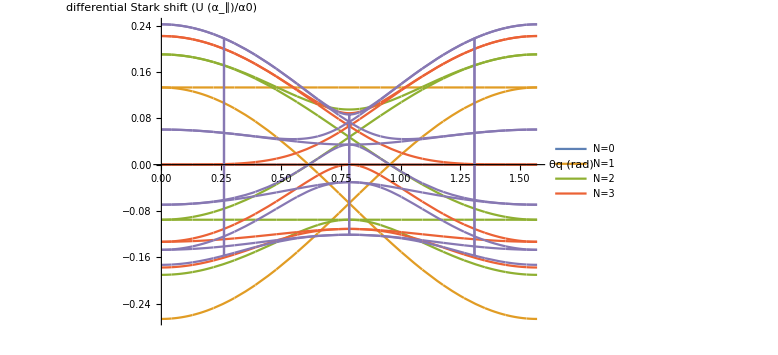

```mathematica
Plot[{evals0,evals1,evals2,evals3,evals4},{θq,0,π/2},PlotLegends->{"N=0","N=1","N=2","N=3"},ImageSize->Large,AxesLabel->{"θq (rad)","differential Stark shift (U (α_∥)/α0)"}]
```

```mathematica
[evals4]
```

{1/231 (-10+3 √(50+14 Cos[4 θq])),1/231 (-10-3 √(50+14 Cos[4 θq])),1/231 (5-15 Cos[2 θq]-6 √(15-10 Cos[2 θq]+11 Cos[4 θq])),1/231 (5-15 Cos[2 θq]+6 √(15-10 Cos[2 θq]+11 Cos[4 θq])),1/231 (5+15 Cos[2 θq]-6 √(15+10 Cos[2 θq]+11 Cos[4 θq])),1/231 (5+15 Cos[2 θq]+6 √(15+10 Cos[2 θq]+11 Cos[4 θq])),1/462 ⅇ^(-6 ⅈ θq) Root[-125440 ⅇ^(18 ⅈ θq)-161280 ⅇ^(18 ⅈ θq) Cos[4 θq]+(-6240 ⅇ^(12 ⅈ θq)-3744 ⅇ^(12 ⅈ θq) Cos[4 θq]) #1+#1^3&,1],1/462 ⅇ^(-6 ⅈ θq) Root[-125440 ⅇ^(18 ⅈ θq)-161280 ⅇ^(18 ⅈ θq) Cos[4 θq]+(-6240 ⅇ^(12 ⅈ θq)-3744 ⅇ^(12 ⅈ θq) Cos[4 θq]) #1+#1^3&,2],1/462 ⅇ^(-6 ⅈ θq) Root[-125440 ⅇ^(18 ⅈ θq)-161280 ⅇ^(18 ⅈ θq) Cos[4 θq]+(-6240 ⅇ^(12 ⅈ θq)-3744 ⅇ^(12 ⅈ θq) Cos[4 θq]) #1+#1^3&,3]}

```mathematica
evals0=Eigenvalues[HacNs[[1+0]]];
evals1=Eigenvalues[HacNs[[1+1]]];
evals2=Eigenvalues[HacNs[[1+2]]];
evals3=Eigenvalues[HacNs[[1+3]]];
evals4=Eigenvalues[HacNs[[1+4]]];
evals5=Eigenvalues[HacNs[[1+5]]];
evals6=Eigenvalues[HacNs[[1+6]]];
d0=ParallelTable[Re[N[evals0/.θq->q]],{q,0+10^-5,π+10^-5,π/64}]ᵀ;
d1=ParallelTable[Re[N[evals1/.θq->q]],{q,0+10^-5,π+10^-5,π/64}]ᵀ;
d2=ParallelTable[Re[N[evals2/.θq->q]],{q,0+10^-5,π+10^-5,π/64}]ᵀ;
d3=ParallelTable[Re[N[evals3/.θq->q]],{q,0+10^-5,π+10^-5,π/64}]ᵀ;
d4=ParallelTable[Re[N[evals4/.θq->q]],{q,0+10^-5,π+10^-5,π/64}]ᵀ;
d5=ParallelTable[Re[N[evals5/.θq->q]],{q,0+10^-5,π+10^-5,π/64}]ᵀ;
d6=ParallelTable[Re[N[evals6/.θq->q]],{q,0+10^-5,π+10^-5,π/64}]ᵀ;
```

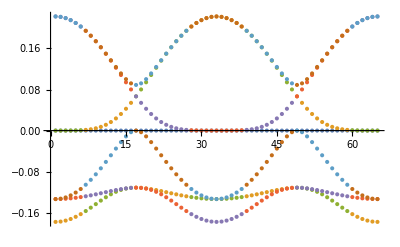

```mathematica
ListPlot[d3,Joined->False]
```

```mathematica
t=Abs[yℋ1[[nRanges[[7]]]].{0,0,0,1,0,0,0,0,0,1,0,0,0}]^2
```

Abs[1/32 ⅇ^(-3 ⅈ ϕ) √(1365/π) Cos[θ] (-3+11 Cos[θ]^2) Sin[θ]^3-1/32 ⅇ^(3 ⅈ ϕ) √(1365/π) Cos[θ] (-3+11 Cos[θ]^2) Sin[θ]^3]^2

```mathematica
SphericalPlot3D[t,{θ,0,π},{ϕ,0,2π},PlotRange->All]
```

-Graphics3D-

```mathematica
%[[1]]
```

{1/231 (5-15 Cos[2 θq]-6 √(15-10 Cos[2 θq]+11 Cos[4 θq])),1/231 (5-15 Cos[2 θq]+6 √(15-10 Cos[2 θq]+11 Cos[4 θq])),1/231 (5+15 Cos[2 θq]-6 √(15+10 Cos[2 θq]+11 Cos[4 θq])),1/231 (5+15 Cos[2 θq]+6 √(15+10 Cos[2 θq]+11 Cos[4 θq])),1/231 (-10+3 √(50+14 Cos[4 θq])),1/231 (-10-3 √(50+14 Cos[4 θq])),1/462 ⅇ^(-4 ⅈ (2 θh+θq)) Root[-80640 ⅇ^(24 ⅈ θh+8 ⅈ θq)-125440 ⅇ^(24 ⅈ θh+12 ⅈ θq)-80640 ⅇ^(24 ⅈ θh+16 ⅈ θq)+(-1872 ⅇ^(16 ⅈ θh+4 ⅈ θq)-6240 ⅇ^(16 ⅈ θh+8 ⅈ θq)-1872 ⅇ^(16 ⅈ θh+12 ⅈ θq)) #1+#1^3&,1],1/462 ⅇ^(-4 ⅈ (2 θh+θq)) Root[-80640 ⅇ^(24 ⅈ θh+8 ⅈ θq)-125440 ⅇ^(24 ⅈ θh+12 ⅈ θq)-80640 ⅇ^(24 ⅈ θh+16 ⅈ θq)+(-1872 ⅇ^(16 ⅈ θh+4 ⅈ θq)-6240 ⅇ^(16 ⅈ θh+8 ⅈ θq)-1872 ⅇ^(16 ⅈ θh+12 ⅈ θq)) #1+#1^3&,2],1/462 ⅇ^(-4 ⅈ (2 θh+θq)) Root[-80640 ⅇ^(24 ⅈ θh+8 ⅈ θq)-125440 ⅇ^(24 ⅈ θh+12 ⅈ θq)-80640 ⅇ^(24 ⅈ θh+16 ⅈ θq)+(-1872 ⅇ^(16 ⅈ θh+4 ⅈ θq)-6240 ⅇ^(16 ⅈ θh+8 ⅈ θq)-1872 ⅇ^(16 ⅈ θh+12 ⅈ θq)) #1+#1^3&,3]}

```mathematica
eigs[2]
```

{{-2/21,1/21 (1-3 Cos[2 θq]),1/21 (1+3 Cos[2 θq]),-1/21 ⅇ^(-2 ⅈ θq) √(3+ⅇ^(4 ⅈ θq)) √(1+3 ⅇ^(4 ⅈ θq)),1/21 ⅇ^(-2 ⅈ θq) √(3+ⅇ^(4 ⅈ θq)) √(1+3 ⅇ^(4 ⅈ θq))},{{-ⅇ^(-8 ⅈ θh+4 ⅈ θq),0,0,0,1},{0,-ⅇ^(-4 ⅈ θh+2 ⅈ θq),0,1,0},{0,ⅇ^(-4 ⅈ θh+2 ⅈ θq),0,1,0},{ⅇ^(-8 ⅈ θh+4 ⅈ θq),0,-(ⅇ^(-4 ⅈ θh) (-2 ⅇ^(2 ⅈ θq)+√(3+10 ⅇ^(4 ⅈ θq)+3 ⅇ^(8 ⅈ θq))) Sec[2 θq])/(√6),0,1},{ⅇ^(-8 ⅈ θh+4 ⅈ θq),0,(ⅇ^(-4 ⅈ θh) (2 ⅇ^(2 ⅈ θq)+√(3+10 ⅇ^(4 ⅈ θq)+3 ⅇ^(8 ⅈ θq))) Sec[2 θq])/(√6),0,1}}}

```mathematica
{evals,evecs}=Eigensystem[HacNs[[1+3]]];
evals=FullSimplify[PowerExpand[FullSimplify[evals,Assumptions->{0<=θh<2π,0<=θq<2π}]],Assumptions->{0<=θh<2π,0<=θq<2π}];
evecs=FullSimplify[evecs,Assumptions->{0<=θh<2π,0<=θq<2π}];
```

```mathematica
evals
```

{0,1/45 (-1-3 Cos[2 θq]-2 √(7-6 Cos[2 θq]+3 Cos[4 θq])),1/45 (-1-3 Cos[2 θq]+2 √(7-6 Cos[2 θq]+3 Cos[4 θq])),1/45 (-1+3 Cos[2 θq]-2 √(7+6 Cos[2 θq]+3 Cos[4 θq])),1/45 (-1+3 Cos[2 θq]+2 √(7+6 Cos[2 θq]+3 Cos[4 θq])),1/45 (2-√(34+30 Cos[4 θq])),1/45 (2+√(34+30 Cos[4 θq]))}

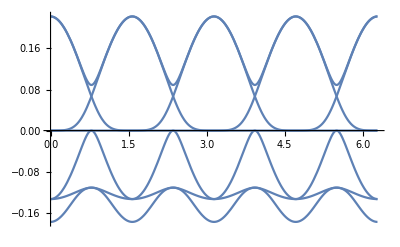

```mathematica
Plot[evals/.θh->0,{θq,0,2π}]
```

```mathematica
f[θh_,θq_]=Abs[evecs[[1]].yℋ1[[nRanges[[1+3]]]]]^2;
Manipulate[SphericalPlot3D[f[θh,θq],{θ,0,π},{ϕ,0,2π},PlotRange->All],{θh,0,π},{θq,0,π}]
```

# Stop

```mathematica
{evalsAC,evecsAC}=Eigensystem[Hacℋ1]//FullSimplify;
```

```mathematica
{θh,θq}/.constants
```

{1/2 (π-ArcCos[1/(√3)]),π/2-ArcCos[1/(√3)]}

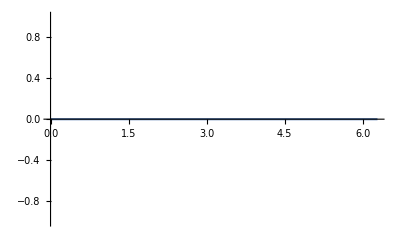

```mathematica
sel=Select[lℋ1,#[[1]]==3&];
pos=Flatten[Position[lℋ1,#]&/@sel];
{evals,evecs}=FullSimplify[Eigensystem[Hacℋ1[[pos,pos]]]];
evals=FullSimplify[α0/(U Δ)evals,Assumptions->{α0>0,U>0,Δ>0}];
Plot[evals,{θq,0,2π}]
```

```mathematica
FullSimplify[evals,Assumptions->{0<θh>2π,0<θq<2π}]
```

{0,1/45 (-1-3 Cos[2 θq]-2 ⅇ^(-2 ⅈ (4 θh+θq)) √(ⅇ^(4 ⅈ (4 θh+θq)) (7-6 Cos[2 θq]+3 Cos[4 θq]))),1/45 (-1-3 Cos[2 θq]+2 ⅇ^(-2 ⅈ (4 θh+θq)) √(ⅇ^(4 ⅈ (4 θh+θq)) (7-6 Cos[2 θq]+3 Cos[4 θq]))),1/45 (-1+3 Cos[2 θq]-2 ⅇ^(-2 ⅈ (4 θh+θq)) √(ⅇ^(4 ⅈ (4 θh+θq)) (7+6 Cos[2 θq]+3 Cos[4 θq]))),1/45 (-1+3 Cos[2 θq]+2 ⅇ^(-2 ⅈ (4 θh+θq)) √(ⅇ^(4 ⅈ (4 θh+θq)) (7+6 Cos[2 θq]+3 Cos[4 θq]))),1/45 (2-ⅇ^(-2 ⅈ (4 θh+θq)) √(ⅇ^(16 ⅈ θh) (5+3 ⅇ^(4 ⅈ θq)) (3+5 ⅇ^(4 ⅈ θq)))),1/45 (2+ⅇ^(-2 ⅈ (4 θh+θq)) √(ⅇ^(16 ⅈ θh) (5+3 ⅇ^(4 ⅈ θq)) (3+5 ⅇ^(4 ⅈ θq))))}

```mathematica
evecs[[1]]
```

{0,-ⅇ^(-8 ⅈ θh+4 ⅈ θq),0,0,0,1,0}

```mathematica
FullSimplify[evals,Assumptions->α0>0]
```

{0,1/45 (-1-3 Cos[2 θq]-2 ⅇ^(-2 ⅈ (4 θh+θq)) √(ⅇ^(4 ⅈ (4 θh+θq)) (7-6 Cos[2 θq]+3 Cos[4 θq]))),1/45 (-1-3 Cos[2 θq]+2 ⅇ^(-2 ⅈ (4 θh+θq)) √(ⅇ^(4 ⅈ (4 θh+θq)) (7-6 Cos[2 θq]+3 Cos[4 θq]))),1/45 (-1+3 Cos[2 θq]-2 ⅇ^(-2 ⅈ (4 θh+θq)) √(ⅇ^(4 ⅈ (4 θh+θq)) (7+6 Cos[2 θq]+3 Cos[4 θq]))),1/45 (-1+3 Cos[2 θq]+2 ⅇ^(-2 ⅈ (4 θh+θq)) √(ⅇ^(4 ⅈ (4 θh+θq)) (7+6 Cos[2 θq]+3 Cos[4 θq]))),1/45 (2-ⅇ^(-2 ⅈ (4 θh+θq)) √(ⅇ^(16 ⅈ θh) (5+3 ⅇ^(4 ⅈ θq)) (3+5 ⅇ^(4 ⅈ θq)))),1/45 (2+ⅇ^(-2 ⅈ (4 θh+θq)) √(ⅇ^(16 ⅈ θh) (5+3 ⅇ^(4 ⅈ θq)) (3+5 ⅇ^(4 ⅈ θq))))}

{{-(2 U Δ)/(21 α0),-(ⅇ^(-2 ⅈ θq) (3-2 ⅇ^(2 ⅈ θq)+3 ⅇ^(4 ⅈ θq)) U Δ)/(42 α0),(ⅇ^(-2 ⅈ θq) (3+2 ⅇ^(2 ⅈ θq)+3 ⅇ^(4 ⅈ θq)) U Δ)/(42 α0),-(ⅇ^(-2 ⅈ θq) √(3+10 ⅇ^(4 ⅈ θq)+3 ⅇ^(8 ⅈ θq)) U Δ)/(21 α0),(ⅇ^(-2 ⅈ θq) √(3+10 ⅇ^(4 ⅈ θq)+3 ⅇ^(8 ⅈ θq)) U Δ)/(21 α0)},{{-1/2 ⅇ^(-8 ⅈ θh+2 ⅈ θq) (1+ⅇ^(4 ⅈ θq)) Sec[2 θq],0,0,0,1},{0,-ⅇ^(-4 ⅈ θh+2 ⅈ θq),0,1,0},{0,ⅇ^(-4 ⅈ θh+2 ⅈ θq),0,1,0},{1/2 ⅇ^(-8 ⅈ θh) (1+ⅇ^(4 ⅈ θq)) Sec[2 θq] (-ⅇ^(2 ⅈ θq)+Sec[2 θq]+ⅇ^(4 ⅈ θq) Sec[2 θq]),0,-(ⅇ^(-4 ⅈ θh) (-2 ⅇ^(2 ⅈ θq)+√(3+10 ⅇ^(4 ⅈ θq)+3 ⅇ^(8 ⅈ θq))) Sec[2 θq])/(√6),0,1},{1/2 ⅇ^(-8 ⅈ θh) (1+ⅇ^(4 ⅈ θq)) Sec[2 θq] (-ⅇ^(2 ⅈ θq)+Sec[2 θq]+ⅇ^(4 ⅈ θq) Sec[2 θq]),0,(ⅇ^(-4 ⅈ θh) (2 ⅇ^(2 ⅈ θq)+√(3+10 ⅇ^(4 ⅈ θq)+3 ⅇ^(8 ⅈ θq))) Sec[2 θq])/(√6),0,1}}}

```mathematica
Position[lℋ1,{{0,0},{1,0}}]
```

{}

```mathematica
dd
```

```mathematica
Hacℋ1[[]]
```

-(U Δ)/(15 α0)

```mathematica
evecsAC/.
```

{{0,0,0,0,0,0,0,0,0,0,-ⅇ^(-8 ⅈ θh+4 ⅈ θq),0,0,0,1,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,-ⅇ^(-8 ⅈ θh+4 ⅈ θq),0,0,0,1,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,-ⅇ^(-4 ⅈ θh+2 ⅈ θq),0,1,0,0,0,0,0,0,0,0},{0,ⅇ^(-4 ⅈ θh+2 ⅈ θq),0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,-ⅇ^(-4 ⅈ θh+2 ⅈ θq),0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,ⅇ^(-4 ⅈ θh+2 ⅈ θq),0,1,0,0,0,0,0,0,0,0},{0,0,0,0,ⅇ^(-8 ⅈ θh+4 ⅈ θq),0,-(ⅇ^(-4 ⅈ θh) (-2 ⅇ^(2 ⅈ θq)+√(3+10 ⅇ^(4 ⅈ θq)+3 ⅇ^(8 ⅈ θq))) Sec[2 θq])/(√6),0,1,0,0,0,0,0,0,0},{0,0,0,0,ⅇ^(-8 ⅈ θh+4 ⅈ θq),0,(ⅇ^(-4 ⅈ θh) (2 ⅇ^(2 ⅈ θq)+√(3+10 ⅇ^(4 ⅈ θq)+3 ⅇ^(8 ⅈ θq))) Sec[2 θq])/(√6),0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,-ⅇ^(-12 ⅈ θh+6 ⅈ θq),0,(ⅇ^(-2 ⅈ (10 θh+θq)) (2 ⅇ^(4 ⅈ (3 θh+2 θq)) α0^5 (-4+3 Cos[2 θq])-4 √(-ⅇ^(8 ⅈ (3 θh+2 θq)) α0^10 (-7+6 Cos[2 θq]-3 Cos[4 θq]))))/(√15 (1+ⅇ^(4 ⅈ θq)) α0^5),0,(ⅇ^(-2 ⅈ (8 θh+3 θq)) (2 √(-ⅇ^(8 ⅈ (3 θh+2 θq)) α0^10 (-7+6 Cos[2 θq]-3 Cos[4 θq])) Sec[2 θq]+ⅇ^(4 ⅈ (3 θh+2 θq)) α0^5 (-3+4 Sec[2 θq])))/(√15 α0^5),0,1},{0,0,0,0,0,0,0,0,0,-ⅇ^(-12 ⅈ θh+6 ⅈ θq),0,(ⅇ^(-2 ⅈ (10 θh+θq)) (2 ⅇ^(4 ⅈ (3 θh+2 θq)) α0^5 (-4+3 Cos[2 θq])+4 √(-ⅇ^(8 ⅈ (3 θh+2 θq)) α0^10 (-7+6 Cos[2 θq]-3 Cos[4 θq]))))/(√15 (1+ⅇ^(4 ⅈ θq)) α0^5),0,(ⅇ^(-2 ⅈ (8 θh+3 θq)) (-2 √(-ⅇ^(8 ⅈ (3 θh+2 θq)) α0^10 (-7+6 Cos[2 θq]-3 Cos[4 θq])) Sec[2 θq]+ⅇ^(4 ⅈ (3 θh+2 θq)) α0^5 (-3+4 Sec[2 θq])))/(√15 α0^5),0,1},{0,0,0,0,0,0,0,0,0,ⅇ^(-12 ⅈ θh+6 ⅈ θq),0,(ⅇ^(-2 ⅈ (10 θh+θq)) (2 ⅇ^(4 ⅈ (3 θh+2 θq)) α0^5 (4+3 Cos[2 θq])-4 √(ⅇ^(8 ⅈ (3 θh+2 θq)) α0^10 (7+6 Cos[2 θq]+3 Cos[4 θq]))))/(√15 (1+ⅇ^(4 ⅈ θq)) α0^5),0,(ⅇ^(-2 ⅈ (8 θh+3 θq)) (-2 √(ⅇ^(8 ⅈ (3 θh+2 θq)) α0^10 (7+6 Cos[2 θq]+3 Cos[4 θq])) Sec[2 θq]+ⅇ^(4 ⅈ (3 θh+2 θq)) α0^5 (3+4 Sec[2 θq])))/(√15 α0^5),0,1},{0,0,0,0,0,0,0,0,0,ⅇ^(-12 ⅈ θh+6 ⅈ θq),0,(ⅇ^(-2 ⅈ (10 θh+θq)) (2 ⅇ^(4 ⅈ (3 θh+2 θq)) α0^5 (4+3 Cos[2 θq])+4 √(ⅇ^(8 ⅈ (3 θh+2 θq)) α0^10 (7+6 Cos[2 θq]+3 Cos[4 θq]))))/(√15 (1+ⅇ^(4 ⅈ θq)) α0^5),0,(ⅇ^(-2 ⅈ (8 θh+3 θq)) (2 √(ⅇ^(8 ⅈ (3 θh+2 θq)) α0^10 (7+6 Cos[2 θq]+3 Cos[4 θq])) Sec[2 θq]+ⅇ^(4 ⅈ (3 θh+2 θq)) α0^5 (3+4 Sec[2 θq])))/(√15 α0^5),0,1},{0,0,0,0,0,0,0,0,0,0,ⅇ^(-8 ⅈ θh+4 ⅈ θq),0,-(ⅇ^(-2 ⅈ (8 θh+3 θq)) (-2 ⅇ^(4 ⅈ (3 θh+2 θq)) α0^5+√(ⅇ^(12 ⅈ (2 θh+θq)) (5+3 ⅇ^(4 ⅈ θq)) (3+5 ⅇ^(4 ⅈ θq)) α0^10)) Sec[2 θq])/(√30 α0^5),0,1,0},{0,0,0,0,0,0,0,0,0,0,ⅇ^(-8 ⅈ θh+4 ⅈ θq),0,(ⅇ^(-2 ⅈ (8 θh+3 θq)) (2 ⅇ^(4 ⅈ (3 θh+2 θq)) α0^5+√(ⅇ^(12 ⅈ (2 θh+θq)) (5+3 ⅇ^(4 ⅈ θq)) (3+5 ⅇ^(4 ⅈ θq)) α0^10)) Sec[2 θq])/(√30 α0^5),0,1,0}}

## Results

### Find AC eigenstates

```mathematica
evecsACn={(Normalize/@(evecsAC/.constants//N//Chop))[[#]]}ᵀ&/@Range[nℋ1];
evalsACn=Chop[QuantityMagnitude[UnitConvert[evalsAC/h//.constants]],10^-9];
```

```mathematica
evalsACn
```

{0,0,-1.43059×10^6,2.00283×10^6,0,0,-2.00283×10^6,1.43059×10^6,-1.6519×10^6,1.6519×10^6,422592.,-1.75781×10^6,-1.72376×10^6,1.72376×10^6,-422592.+2.79679×10^-9 ⅈ,1.75781×10^6-2.79679×10^-9 ⅈ}

```mathematica
evalsAC
```

{0,0,-(2 U Δ)/(21 α0),(2 U Δ)/(15 α0),(U Δ (1-3 Cos[2 θq]))/(21 α0),(U Δ (-1+3 Cos[2 θq]))/(15 α0),-(U Δ (1+3 Cos[2 θq]))/(15 α0),(U Δ (1+3 Cos[2 θq]))/(21 α0),-(ⅇ^(-2 ⅈ θq) √((3+ⅇ^(4 ⅈ θq)) (1+3 ⅇ^(4 ⅈ θq))) U Δ)/(21 α0),(ⅇ^(-2 ⅈ θq) √((3+ⅇ^(4 ⅈ θq)) (1+3 ⅇ^(4 ⅈ θq))) U Δ)/(21 α0),-(U Δ (α0^5+3 α0^5 Cos[2 θq]-2 ⅇ^(-4 ⅈ (3 θh+2 θq)) √(-ⅇ^(8 ⅈ (3 θh+2 θq)) α0^10 (-7+6 Cos[2 θq]-3 Cos[4 θq]))))/(45 α0^6),-(U Δ (α0^5+3 α0^5 Cos[2 θq]+2 ⅇ^(-4 ⅈ (3 θh+2 θq)) √(-ⅇ^(8 ⅈ (3 θh+2 θq)) α0^10 (-7+6 Cos[2 θq]-3 Cos[4 θq]))))/(45 α0^6),-(U Δ (α0^5-3 α0^5 Cos[2 θq]+2 ⅇ^(-4 ⅈ (3 θh+2 θq)) √(ⅇ^(8 ⅈ (3 θh+2 θq)) α0^10 (7+6 Cos[2 θq]+3 Cos[4 θq]))))/(45 α0^6),-(U Δ (α0^5-3 α0^5 Cos[2 θq]-2 ⅇ^(-4 ⅈ (3 θh+2 θq)) √(ⅇ^(8 ⅈ (3 θh+2 θq)) α0^10 (7+6 Cos[2 θq]+3 Cos[4 θq]))))/(45 α0^6),(U (2 α0^5-ⅇ^(-4 ⅈ (3 θh+2 θq)) √(ⅇ^(12 ⅈ (2 θh+θq)) (5+3 ⅇ^(4 ⅈ θq)) (3+5 ⅇ^(4 ⅈ θq)) α0^10)) Δ)/(45 α0^6),(U (2 α0^5+ⅇ^(-4 ⅈ (3 θh+2 θq)) √(ⅇ^(12 ⅈ (2 θh+θq)) (5+3 ⅇ^(4 ⅈ θq)) (3+5 ⅇ^(4 ⅈ θq)) α0^10)) Δ)/(45 α0^6)}

```mathematica
Solve[(ⅇ^(-2 ⅈ θq) √((3+ⅇ^(4 ⅈ θq)) (1+3 ⅇ^(4 ⅈ θq))) U Δ)/(21 α0)==0,θq]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{θq→-1/4 ⅈ (ⅈ π-Log[3])},{θq→-1/4 ⅈ (ⅈ π+Log[3])},{θq→-ⅈ Log[-(-3)^(1/4)]},{θq→-ⅈ Log[-ⅈ (-3)^(1/4)]},{θq→-ⅈ Log[ⅈ (-3)^(1/4)]},{θq→-ⅈ Log[-(-1/3)^(1/4)]},{θq→-ⅈ Log[-(-1)^(3/4)/3^(1/4)]},{θq→-ⅈ Log[(-1)^(3/4)/3^(1/4)]}}

```mathematica
ⅇ^(-4 ⅈ θq)(3+ⅇ^(4 ⅈ θq)) (1+3 ⅇ^(4 ⅈ θq))//FullSimplify
```

10+6 Cos[4 θq]

```mathematica
Solve[10+6 Cos[4 θq]==0,θq]
```

{{θq→ConditionalExpression[1/4 (-ArcCos[-5/3]+2 π C[1]), C[1]∈ℤ]},{θq→ConditionalExpression[1/4 (ArcCos[-5/3]+2 π C[1]), C[1]∈ℤ]}}

```mathematica
1/4 (-ArcCos[-5/3])180/π//N
```

-45.+15.7365 ⅈ

```mathematica
Cos[2 θq]
```

Cos[2 θq]